{{1,-1.9680.019},{2,-2.4970.019},{3,-3.1330.025},{4,-3.7240.029},{5,-3.9230.032},{6,-3.9000.030},{7,-3.7620.025},{8,-3.7960.029},{9,-3.6850.027},{10,-3.7350.029}}

{{1,-2.1950.016},{2,-2.4330.017},{3,-2.3450.015},{4,-2.3650.016},{5,-2.3580.017},{6,-2.1890.015},{7,-2.0480.016},{8,-1.9370.015},{9,-1.7190.018},{10,-1.5890.015}}

{{1,-1.7770.013},{2,-1.8990.012},{3,-2.0630.014},{4,-2.0860.013},{5,-2.3070.013},{6,-2.5370.012},{7,-2.4940.013},{8,-2.5630.013},{9,-2.6900.013},{10,-2.6290.013}}

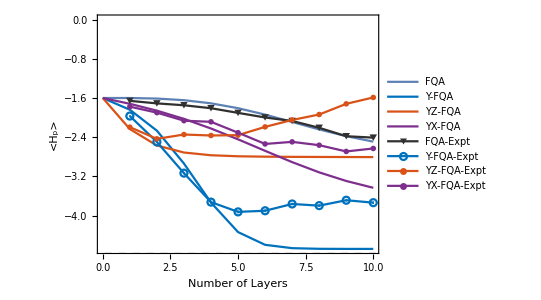

```mathematica
dataF={-1.6000000000000003,-1.6,-1.6112186988051767,-1.6443679258190123,-1.7083184185777482,-1.8074843875028677,-1.9385975788191365,-2.089294725356276,-2.2413472146032403,-2.3779707558615923,-2.49004185355962};
dataFCDyz={-1.6000000000000003,-2.2334470495899725,-2.5684083828392423,-2.7120386006966477,-2.767704374147625,-2.7886639605780035,-2.796901117668267,-2.800578573771387,-2.802597839473322,-2.8040150338739207,-2.8052546529514255};
dataFCDyx={-1.6000000000000003,-1.7181717682385587,-1.8581932932739278,-2.02558432100301,-2.2220256338980735,-2.4431561925077867,-2.677433835549765,-2.9078152120628245,-3.116836552173917,-3.2926242115193656,-3.431801610429116};
dataFCDy={-1.6000000000000003,-1.8392700229319439,-2.2666712462333316,-2.936265422867532,-3.732462126362557,-4.335154531302772,-4.59504045908713,-4.663320886131266,-4.676413580330181,-4.678384780480009,-4.6785644797493005};
dataExpFP={-1.65813688,-1.70954942,-1.74790162,-1.80807361,-1.90327266,-1.99694031,-2.06863802,-2.20754986,-2.37958891,-2.40821412};
dataExpFPstd={0.01608872,0.01624803,0.01722424,0.0150883,0.01443058,0.0142882,0.01418565,0.0145655,0.01632037,0.01787288};
dataExpFCDyP={-1.96755175,-2.49655151,-3.13282555,-3.72381233,-3.9230051,-3.90015401,-3.76191677,-3.79570882,-3.68542535,-3.73513478};
dataExpFCDyPstd={0.01882895,0.01912995,0.02474806,0.02911224,0.03192573,0.02979792,0.02475307,0.02878631,0.02684144,0.02869299};
dataExpFCDyzP={-2.19451691,-2.43306042,-2.34502538,-2.36456698,-2.35783729,-2.18884156,-2.04793886,-1.93654512,-1.71872006,-1.58866838};
dataExpFCDyzPstd={0.01602453,0.01665156,0.01521476,0.01593135,0.01702451,0.01514654,0.01602922,0.01496045,0.01813687,0.01531789};
dataExpFCDyxP={-1.77667554,-1.89856763,-2.06269785,-2.08559436,-2.3072449,-2.53715584,-2.49445766,-2.56255552,-2.69007195,-2.62947978};
dataExpFCDyxPstd={0.01315731,0.01196343,0.01416707,0.01251447,0.01253824,0.01240699,0.0128687,0.01286127,0.01268407,0.01273414};
dataExpFPp=Table[{i,Around[dataExpFP[[i]],dataExpFPstd[[i]]]},{i,Length[dataExpFP]}];
dataExpFCDyPp=Table[{i,Around[dataExpFCDyP[[i]],dataExpFCDyPstd[[i]]]},{i,Length[dataExpFP]}]
dataExpFCDyzPp=Table[{i,Around[dataExpFCDyzP[[i]],dataExpFCDyzPstd[[i]]]},{i,Length[dataExpFP]}]
dataExpFCDyxPp=Table[{i,Around[dataExpFCDyxP[[i]],dataExpFCDyxPstd[[i]]]},{i,Length[dataExpFP]}]
dataFp=Table[{i-1,dataF[[i]]},{i,Length[dataF]}];
dataFCDyP=Table[{i-1,dataFCDy[[i]]},{i,Length[dataFCDy]}];
dataFCDyzP=Table[{i-1,dataFCDyz[[i]]},{i,Length[dataFCDyz]}];
dataFCDyxP=Table[{i-1,dataFCDyx[[i]]},{i,Length[dataFCDyx]}];
Show[ListPlot[{dataFp,dataFCDyP,dataFCDyzP,dataFCDyxP,dataExpFPp,dataExpFCDyPp,dataExpFCDyzPp,dataExpFCDyxPp},PlotRange->All,Joined->{True,True,True,True,True,True,True,True},PlotMarkers->{None,None,None,None,Automatic,Automatic,Automatic,Automatic},PlotLegends->{"FQA","Y-FQA","YZ-FQA","YX-FQA","FQA-Expt","Y-FQA-Expt","YZ-FQA-Expt","YX-FQA-Expt"},PlotStyle->{{RGBColor["#303030"]Thin},{RGBColor["#0072BD"],Thin},{RGBColor["#D95319"],Thin},{RGBColor["#7E2F8E"],Thin},{RGBColor["#303030"]},{RGBColor["#0072BD"]},{RGBColor["#D95319"]},{RGBColor["#7E2F8E"]}},Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,FrameLabel->{{HoldForm["<H_p>"],None},{HoldForm["Number of Layers"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]}],Plot[-4.780861320010876,{x,-3,300},PlotStyle->{Gray,Dashed}],AspectRatio->3/4]
```